# BigWham Verifications - Axi3DP0 Kernel

## Penny-shaped crack under uniform and shear loading

## Load Library

```mathematica
PacletDirectoryLoad[NotebookDirectory[]<>"../../../../"]
<<BigWhamLink`
GetFilesDate[]
```

{/Users/alexis/BigWham_Last/interfaces/BigWhamLink/}

BigWhamLink`LTemplate`Classes`

{/Users/alexis/BigWham_Last/interfaces/BigWhamLink/BigWhamLink/Kernel/../LibraryResources/MacOSX-x86-64/HmatExpressions.dylib→Thu 2 Jun 2022 15:41:03GMT+2,/Users/alexis/BigWham_Last/cmake-build-release/libBigWham.a→Thu 2 Jun 2022 15:31:22GMT+2}

## Mesh

```mathematica
R=1.; (* crack radius *)
Ne=100; (* number of elements *)
coor=Table[{R*i/Ne,0.},{i,0,Ne}];
conn=Table[{i,i+1},{i,1,Ne}];
```

## Build H-mat

```mathematica
ker="Axi3DP0";
G=0.5;ν=0.0;Young=2G(1+ν);λ=(Young ν)/((1+ν)(1-2 ν));
maxleaf=12;
eta=4.;
eps=0.0001;
```

```mathematica
h1=toHMatExpr[coor,conn,ker,{Young,ν},maxleaf,eta,eps];//AbsoluteTiming
```

constructor called

Now setting up and constructing the HMatrix ...

HMatrix is now set !

destructor called

{0.011431,Null}

```mathematica
GetCompressionRatio[h1]
GetSize[h1]
numberUnknowns=GetSize[h1][[1]]
numberCollocationPoints=numberUnknowns/2
```

0.6666

{200,200}

200

100

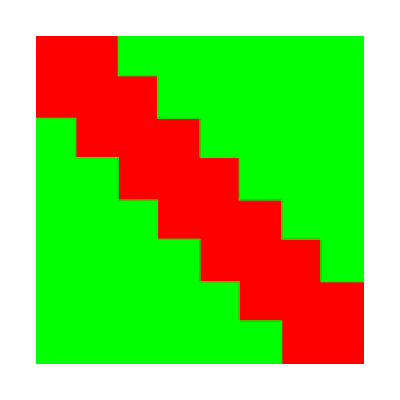

```mathematica
PlotHpattern[h1]
```

## Verification

## Analytical solution

#### Select direction of loading

```mathematica
comp=2;(*{1,2}={shear,normal}*)
```

#### Radial coordinate of nodes (DD) and collocation points

```mathematica
rColl=Table[Mean[coor[[i;;i+1,1]]],{i,Ne}];
rNodes=rColl;
```

#### Analytical solutions functions

```mathematica
P=1; (*Uniform stress magnitude*)
DDsneddon[r_]:=(8 P)/(π (Young/(1-ν^2))) √Abs[R^2-r^2];
DDsegedin[r_]:=(8 (λ+2G) P)/(π G(3 λ+4G)) √Abs[R^2-r^2];

DDanalytical=ConstantArray[0.,numberUnknowns];

If[comp==2,
DDanalytical[[comp;;-1;;2]]=DDsneddon[#]&/@rNodes,
DDanalytical[[comp;;-1;;2]]=DDsegedin[#]&/@rNodes];
```

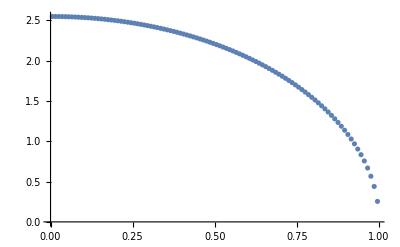

```mathematica
ListPlot[{rNodes,DDanalytical[[comp;;-1;;2]]}//Transpose]
```

### Test H-dot only

```mathematica
tractionNumerical=Hdot[h1,DDanalytical];//RepeatedTiming
```

{0.000029451,Null}

```mathematica
tractionNumerical
```

{0.,0.99912,0.,0.999232,0.,0.999239,0.,0.999241,0.,0.999241,0.,0.999241,0.,0.99924,0.,0.99924,0.,0.999239,0.,0.999238,0.,0.999237,0.,0.999236,0.,0.999235,0.,0.999234,0.,0.999233,0.,0.999231,0.,0.99923,0.,0.999228,0.,0.999226,0.,0.999224,0.,0.999222,0.,0.99922,0.,0.999217,0.,0.999215,0.,0.999212,0.,0.99921,0.,0.999207,0.,0.999204,0.,0.999201,0.,0.999198,0.,0.999194,0.,0.999191,0.,0.999187,0.,0.999183,0.,0.999178,0.,0.999174,0.,0.99917,0.,0.999165,0.,0.99916,0.,0.999155,0.,0.99915,0.,0.999144,0.,0.999138,0.,0.999132,0.,0.999126,0.,0.999119,0.,0.999112,0.,0.999104,0.,0.999097,0.,0.999089,0.,0.99908,0.,0.999071,0.,0.999062,0.,0.999052,0.,0.999042,0.,0.999031,0.,0.99902,0.,0.999008,0.,0.998995,0.,0.998981,0.,0.998967,0.,0.998952,0.,0.998936,0.,0.998919,0.,0.998901,0.,0.998881,0.,0.998861,0.,0.998838,0.,0.998815,0.,0.998789,0.,0.998761,0.,0.998731,0.,0.998699,0.,0.998663,0.,0.998624,0.,0.998582,0.,0.998535,0.,0.998483,0.,0.998424,0.,0.998359,0.,0.998285,0.,0.998202,0.,0.998106,0.,0.997994,0.,0.997864,0.,0.99771,0.,0.997525,0.,0.9973,0.,0.99702,0.,0.996664,0.,0.996199,0.,0.995574,0.,0.994697,0.,0.993402,0.,0.991356,0.,0.987801,0.,0.980704,0.,0.962884,0.,0.89252,0.,-0.545092}

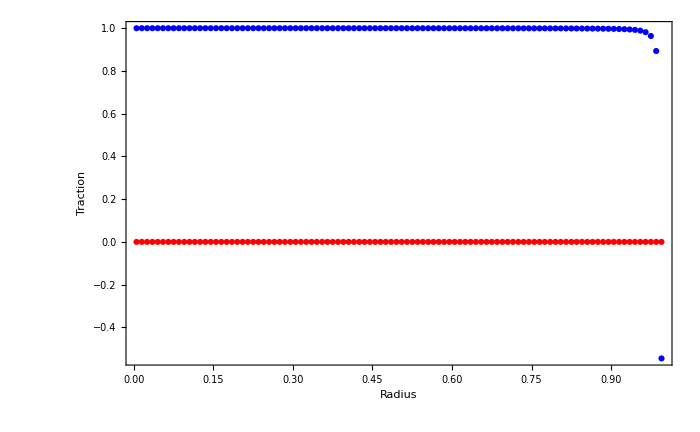

```mathematica
Show[
ListPlot[{rColl,tractionNumerical[[1;;-1;;2]]}//Transpose,PlotMarkers->Automatic,PlotStyle->Red],
ListPlot[{rColl,tractionNumerical[[2;;-1;;2]]}//Transpose,PlotMarkers->Automatic,PlotStyle->Blue],
Frame-> True,BaseStyle->{FontColor->Black,FontSize->22,FontFamily->"Times"},
FrameLabel->(Style[#,FontColor->Black,FontSize->25]& /@{"Radius","Traction"}), 
PlotRange-> All,ImageSize-> 700
]
```

### Test linear solve with H-dot

```mathematica
F=ConstantArray[0.,numberUnknowns];
F[[comp;;-1;;2]]=P;
fdot[x_?(VectorQ[#,NumericQ]&)]:=Hdot[h1,x];
```

```mathematica
{sol,stats}=Reap@LinearSolve[fdot,F,Method->{"Krylov",{"Method"->"BiCGSTAB"(*"GMRES"*)(*"BiCGSTAB"*),(*"Preconditioner"->precJ,"PreconditionerSide"->Right,*)(*"StartingVector"->v0,*)"Tolerance"->10^-5.,"MaxIterations"->1000,"ResidualNormFunction"->((Sow[Norm[#,2]])&)}}];//AbsoluteTiming
```

{0.012034,Null}

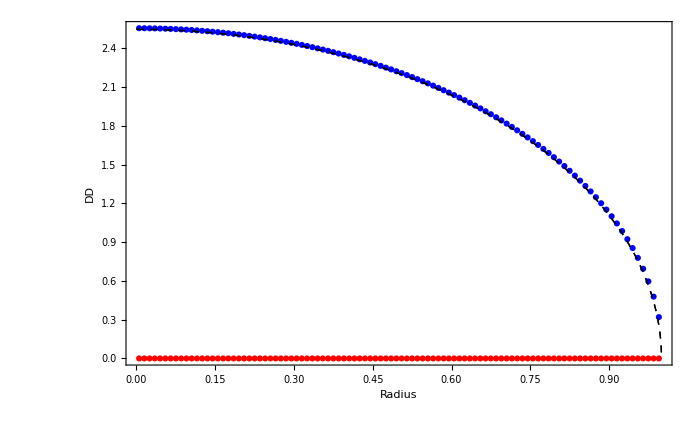

```mathematica
Show[
ListPlot[{rNodes,sol[[1;;-1;;2]]}//Transpose,PlotMarkers->Automatic,PlotStyle->Red],
ListPlot[{rNodes,sol[[2;;-1;;2]]}//Transpose,PlotMarkers->Automatic,PlotStyle->Blue],
Plot[DDsneddon[x],{x,0,1},PlotStyle-> {Black,Dashed,Thick}],
Plot[DDsegedin[x],{x,0,1},PlotStyle-> {Black,Dashed,Thick}],
Frame-> True,BaseStyle->{FontColor->Black,FontSize->22,FontFamily->"Times"},
FrameLabel->(Style[#,FontColor->Black,FontSize->25]& /@{"Radius","DD"}), 
PlotRange-> All,ImageSize-> 700]
```